Possible implementations of network evolution

```mathematica
vi = {vix,viy,0};
via = {vax,vay,0};
vib = {vbx,vby,0};

A = Sqrt[Cross[via,vi].Cross[via,vi]]+Sqrt[Cross[vi,vib].Cross[vi,vib]]+Sqrt[Cross[vib,via].Cross[vib,via]];
ria = vi - via;
rib = vib - vi;
riba =  Sqrt[rib.rib];
riaa = Sqrt[ria.ria];
P =riaa+riba+Sqrt[(rib+ria).(rib+ria)];
En = K/2*(A-a)^2+G/2*P^2+L*(Sqrt[ria.ria]+Sqrt[rib.rib]);

F = -{D[En,vix],D[En,viy]}/. A -> An/.P -> Pn/.(-vay vix+vax viy)/(√(-vay vix+vax viy)^2)-> 1/. (vby vix-vbx viy)/(√(vby vix-vbx viy)^2)-> 1/.1/(√((vbx-vix)^2+(vby-viy)^2))->1/rbi/.1/(√((-vax+vix)^2+(-vay+viy)^2))-> 1/rai;
F/.(vbx-vix)/rbi-> nibx/.(-vax+vix)/rai->- niax/.(vby-viy)/rbi-> niby/.(-vay+viy)/rai->- niay/.K->0
```

{-L (-niax-nibx)-G (-niax-nibx) Pn,-L (-niay-niby)-G (-niay-niby) Pn}

```mathematica
z = {0,0,1};
nA = Cross[z,via-vib]
```

{-vay+vby,vax-vbx,0}

```mathematica
Endev = En/.vix-> vix+dx/.viy-> viy+dy;
```

Now we will consider a set of coefficients and parameters to get the force acting on a vertex on a square.

```mathematica
vu = {-2.5,2.5,0};
va = {2.5,2.5,0};
vb = {-2.5, -2.5,0};
zunit= {0,0,1};

A = 25;
P = 20;
K = 0.006;
A0 = Pi*(5/3)^2;
G = 1;
L = -1;

nA = Cross[ zunit,va-vb];
rua = vu - va;
rbu = vb-vu;
nua = rua/Sqrt[rua.rua];
nbu = rbu/Sqrt[rbu.rbu];
nP = nua-nbu;

F = -K/2*(A-A0)*nA-(G*P+L/2)*nP
```

{19.7441,-19.7441,0.}

```mathematica
{2.5,2.5,0}
```

{2.5,2.5,0}

Exploring the adjacency and Laplace matrices of a graph undergoing a rearrangement

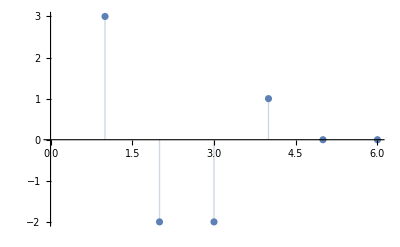

```mathematica
G1 = UndirectedGraph[{1-> 2,1-> 4,1-> 3,2-> 5,2-> 6,4->3,3 -> 6, 6-> 5,5-> 4}];
A1 = AdjacencyMatrix[G1];
Eigenvalues[A1];


G2 = UndirectedGraph[{1-> 2,1-> 4,1-> 5,2-> 3,2-> 6,4->3,3 -> 6, 6-> 5,5-> 4}];
A2 = AdjacencyMatrix[G2];
ListPlot[Eigenvalues[A2],Filling->Axis]
```